# Lab 4: Resource Competition

```mathematica
(* load package *)
<<EcoEvo`
```

EcoEvo Package Version 1.7.2 (September 1, 2023)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

## One resource

Competition between two species (n1 and n2) for one resource (R) in a chemostat.

```mathematica
(* set up model *)
SetModel[{
Pop[n1]->{Equation:>(μ1[R]-m1)n1,Color->Green},
Pop[n2]->{Equation:>(μ2[R]-m2)n2,Color->Darker@Green},
Aux[R]->{Equation:>a(Rin-R)-μ1[R]n1 Q1-μ2[R]n2 Q2,Color->Blue},
Parameters:>{μmax1>0,μmax2>0,H1>0,H2>0,m1>0,m2>0,Q1>0,Q2>0,a>0,Rin>0}
}];

(* growth functions *)
μ1[R_]:=μmax1 R/(R+H1);
μ2[R_]:=μmax2 R/(R+H2);
```

Assign some parameter values and plot f[R] and m.

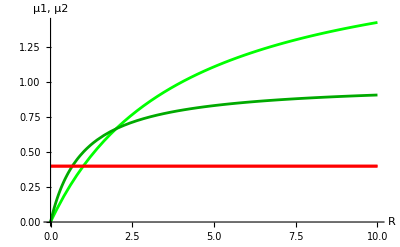

```mathematica
Q1=1;Q2=1; (* quotas = nutrient content per cell *)
μmax1=2;μmax2=1; (* max growth rate *)
H1=4;H2=1; (* half-saturation constant*)
m1=0.4;m2=0.4; (* mortality rate *)

Rstar1:=m1 H1/(μmax1-m1)
Rstar2:=m2 H2/(μmax2-m2)

(* plot growth vs R and mortality *)
Plot[{μ1[R],μ2[R],m1,m2},{R,0,10},PlotStyle->{Color[n1],Color[n2],Red,Red},AxesLabel->{"R","μ1, μ2"}]
```

Now simulate.  What happened?

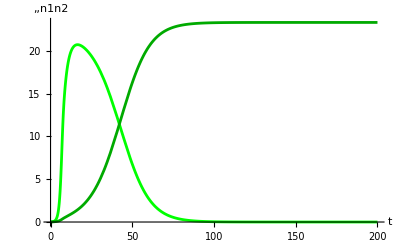

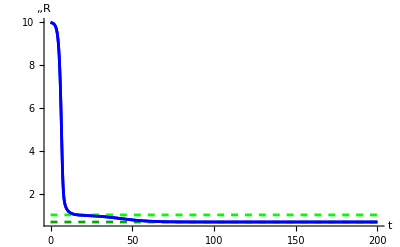

{n1→3.54897×10^-7,n2→23.3333,R→0.666667}

```mathematica
tmax=200;
a=1; (* chemostat dilution rate *)
Rin=10; (* input resource concentration *)

sol=EcoSim[{R->Rin,n1->0.01,n2->0.01},tmax];
PlotDynamics[sol,{n1,n2}]
Show[
PlotDynamics[{sol},{R},PlotRange->{0,All}],
Plot[{Rstar1,Rstar2},{R,0,tmax},PlotStyle->{{Dashed,Color[n1]},{Dashed,Color[n2]}}],
PlotDynamics[{sol},{R}]
]
FinalSlice[sol]
```

What's the effect of mortality rates m on competition?

```mathematica
cross=Solve[μ1[R]==μ2[R],R]
μ1[R/.cross]
```

{{R→0},{R→2}}

{0,2/3}

Neutral outcome when species have equal R*:

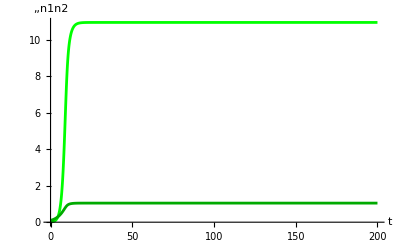

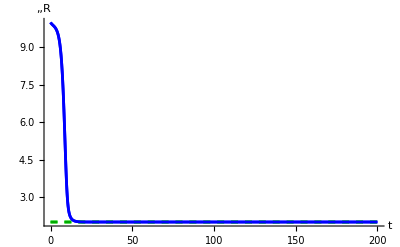

{n1→10.9535,n2→1.04648,R→2.}

```mathematica
m1=m2=2/3;
sol=EcoSim[{R->Rin,n1->0.01,n2->0.1},tmax];
PlotDynamics[sol,{n1,n2}]
Show[
PlotDynamics[{sol},{R},PlotRange->{0,All}],
Plot[{Rstar1,Rstar2},{R,0,tmax},PlotStyle->{{Dashed,Color[n1]},{Dashed,Color[n2]}}],
PlotDynamics[{sol},{R}]
]
FinalSlice[sol]
```

Species 1 wins when mortality rates are above the intersection of the growth curves:

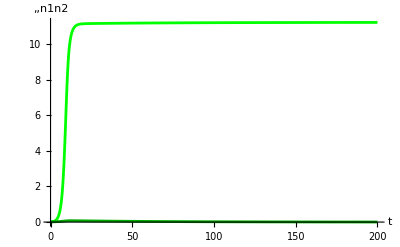

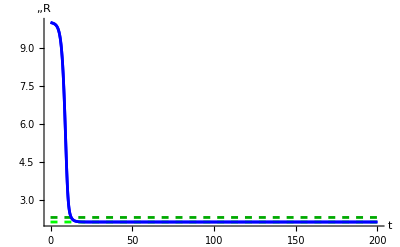

{n1→11.2055,n2→0.00322367,R→2.15387}

```mathematica
m1=m2=0.7;
sol=EcoSim[{R->Rin,n1->0.01,n2->0.01},tmax];
PlotDynamics[sol,{n1,n2}]
Show[
PlotDynamics[{sol},{R},PlotRange->{0,All}],
Plot[{Rstar1,Rstar2},{R,0,tmax},PlotStyle->{{Dashed,Color[n1]},{Dashed,Color[n2]}}],
PlotDynamics[{sol},{R}]
]
FinalSlice[sol]
```

### A few analytical results

```mathematica
ClearParameters
```

There is no coexistence equilibrium:

```mathematica
eq=SolveEcoEq[]
```

{{n1→0,n2→0,R→Rin},{n1→(a (H1 m1+m1 Rin-Rin μmax1))/(m1 Q1 (m1-μmax1)),n2→0,R→-(H1 m1)/(m1-μmax1)},{n1→0,n2→(a (H2 m2+m2 Rin-Rin μmax2))/(m2 Q2 (m2-μmax2)),R→-(H2 m2)/(m2-μmax2)}}

n1 invading the empty system:

```mathematica
Inv[eq[[1]],n1]
```

-m1+(Rin μmax1)/(H1+Rin)

This can be rearranged to see that Rin > R_1^* is needed for species 1 to persist.

n2 invading n1 monoculture:

```mathematica
Inv[eq[[2]],n2]
```

(H2 m2 (m1-μmax1)+H1 m1 (-m2+μmax2))/(H1 m1+H2 (-m1+μmax1))

This can be rearranged to see that R_2^* < R_1^* is needed for species 2 to invade species 1.

## Two essential resources

```mathematica
Clear["Global`*"];
SetModel[{
Aux[R1]->{Equation:>a(R1in-R1)-Q11 Min[μ11 R1,μ12 R2]n1-Q21 Min[μ21 R1,μ22 R2]n2,Color->Blue},
Aux[R2]->{Equation:>a(R2in-R2)-Q12 Min[μ11 R1,μ12 R2]n1-Q22 Min[μ21 R1,μ22 R2]n2,Color->Darker[Blue]},
Pop[n1]->{Equation:>(Min[μ11 R1,μ12 R2]-m1)n1,Color->Green},
Pop[n2]->{Equation:>(Min[μ21 R1,μ22 R2]-m2)n2,Color->Darker[Green]}
}];
```

```mathematica
(* define coex point *)
coexpt:=Which[
Rstar11≤Rstar21&&Rstar22≤Rstar12,{R1->Rstar21,R2->Rstar12},
Rstar11≥Rstar21&&Rstar22≥Rstar12,{R1->Rstar11,R2->Rstar22},
Else,{R1->-1,R2->-1}
];
```

### Stable coexistence

```mathematica
(* Qij = quota of species i of resource j *)
Q11=1;Q12=2;
Q21=2;Q22=1;

(* μij = per R growth rate of species i on resource j *)
μ11=2;μ12=1;
μ21=1;μ22=2;

 (* mi = mortality rate of species i *)
m1=1;
m2=1;

 (* chemostate dilution rate *)
a=1;
```

```mathematica
(* calculate R*'s *)
{Rstar11,Rstar12}={m1/μ11,m1/μ12}
{Rstar21,Rstar22}={m2/μ21,m2/μ22}
```

{1/2,1}

{1,1/2}

Plot ZNGIs and impact vectors.

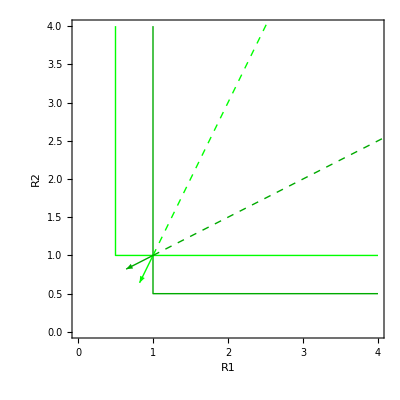

```mathematica
Show[
PlotZNGI[{n1,n2},{R1,0,4},{R2,0,4}],
PlotImpactVector[{R1,R2},{n1,n2},coexpt,Scale->{0.4,-4}],
PlotRange->{{0,4},{0,4}}
]
```

Simulate:

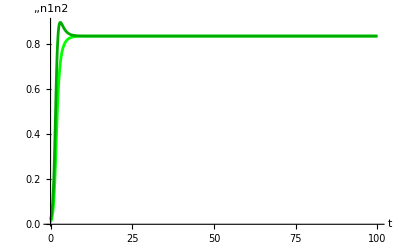

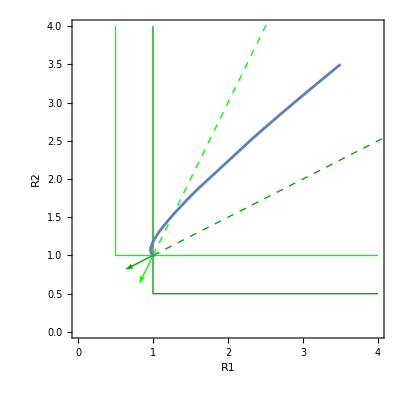

{n1→0.833333,n2→0.833333,R1→1.,R2→1.}

{-2.5,-1.,-1.,-0.833333}

```mathematica
{R1in,R2in}={3.5,3.5};  (* resource supply point *)
sol=EcoSim[{n1->0.01,n2->0.02,R1->R1in,R2->R2in},100];

PlotDynamics[sol,{n1,n2}]

Show[
PlotZNGI[{n1,n2},{R1,0,4},{R2,0,4}],
PlotImpactVector[{R1,R2},{n1,n2},coexpt,Scale->{0.4,-4}],
PlotTrajectory[sol,{R1,R2}],
PlotRange->{{0,4},{0,4}}
]

FinalSlice[sol]
EcoEigenvalues[FinalSlice[sol]]
```

### Founder control (change the Q's)

```mathematica
(* Qij = quota of species i of resource j *)
Q11=2;Q12=1;
Q21=1;Q22=2;

(* μij = per R growth rate of species i on resource j *)
μ11=2;μ12=1;
μ21=1;μ22=2;

 (* mi = mortality rate of species i *)
m1=1;
m2=1;

 (* chemostate dilution rate *)
a=1;
```

```mathematica
(* calculate R*'s *)
{Rstar11,Rstar12}={m1/μ11,m1/μ12}
{Rstar21,Rstar22}={m2/μ21,m2/μ22}
```

{1/2,1}

{1,1/2}

Plot ZNGIs and impact vectors.

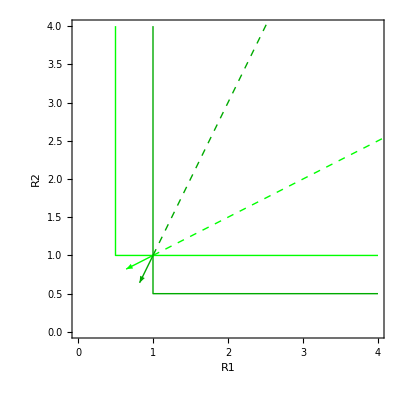

```mathematica
Show[
PlotZNGI[{n1,n2},{R1,0,4},{R2,0,4}],
PlotImpactVector[{R1,R2},{n1,n2},coexpt,Scale->{0.4,-4}],
PlotRange->{{0,4},{0,4}}
]
```

Simulate:

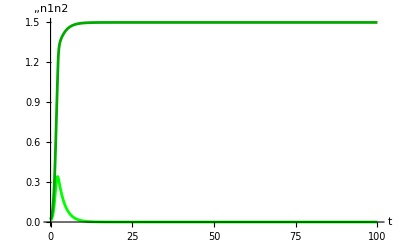

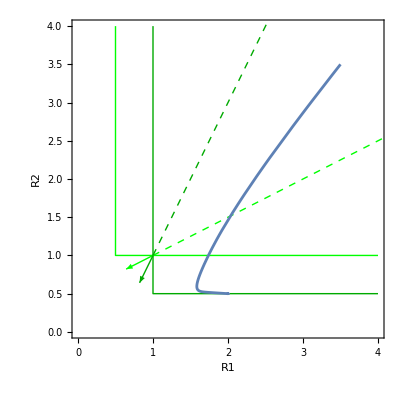

{n1→-1.03561×10^-14,n2→1.5,R1→2.,R2→0.5}

{-6.,-1.,-1.,-0.5}

```mathematica
{R1in,R2in}={3.5,3.5};  (* resource supply point *)
sol=EcoSim[{n1->0.01,n2->0.02,R1->R1in,R2->R2in},100];

PlotDynamics[sol,{n1,n2}]

Show[
PlotZNGI[{n1,n2},{R1,0,4},{R2,0,4}],
PlotImpactVector[{R1,R2},{n1,n2},coexpt,Scale->{0.4,-4}],
PlotTrajectory[sol,{R1,R2}],
PlotRange->{{0,4},{0,4}}
]

FinalSlice[sol]
EcoEigenvalues[FinalSlice[sol]]
```

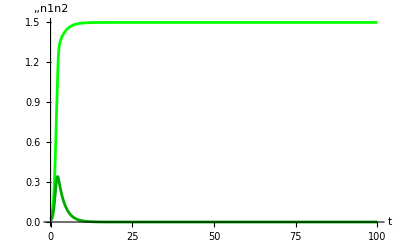

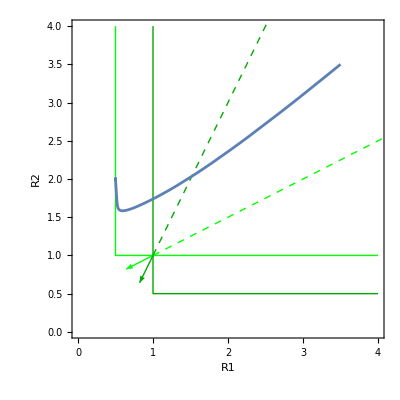

{n1→1.5,n2→-1.04883×10^-14,R1→0.5,R2→2.}

{-6.,-1.,-1.,-0.5}

```mathematica
{R1in,R2in}={3.5,3.5};  (* resource supply point *)
sol=EcoSim[{n1->0.02,n2->0.01,R1->R1in,R2->R2in},100];

PlotDynamics[sol,{n1,n2}]

Show[
PlotZNGI[{n1,n2},{R1,0,4},{R2,0,4}],
PlotImpactVector[{R1,R2},{n1,n2},coexpt,Scale->{0.4,-4}],
PlotTrajectory[sol,{R1,R2}],
PlotRange->{{0,4},{0,4}}
]

FinalSlice[sol]
EcoEigenvalues[FinalSlice[sol]]
```

Outcome depends on initial conditions.